Measurement-Based Quantum Computation |

According to the fundamental postulates of quantum mechanics discussed at the very beginning of the book, the quantum state of a system changes as a consequence of two different causes. One is the time-evolution governed by the Schrödinger equation. Both the dynamical and geometric schemes of quantum computation are inherently based on such time evolution. The other cause for the change in quantum states is the collapse of the quantum states after measurement, as dictated by Postulate 3. So can we also use it for quantum computation? At first glance, it may look absurd when considering the uncontrollable and random nature of the collapse of a quantum state upon measurement. Nevertheless, quantum computation has been recently shown to be possible just by employing measurements in different bases, provided the system is prepared in a special quantum state called the cluster state or, more generally, the graph state (Raussendorf & Briegel, 2001; Raussendorf et al., 2002). Such a scheme of quantum computation is the measurement-based quantum computation or one-way quantum computation. The reasoning behind the “one-way” nomenclature will become clear below. There are several technical methods to implement measurement-based quantum computation. Here, we introduce elementary ideas, and we kindly refer interested readers to the aforementioned articles and their follow-up literature.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this documentation, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Basic Ideas

To get an idea of how the measurement-based scheme works, first consider a quantum circuit of the following simple form.

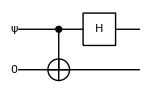

```mathematica
qc1a=QuantumCircuit[
ProductState[S[1,$]->c@{0,1},"Label"->Ket["ψ"]],Ket[S@{2}],
CNOT[S[1,$],S[2,$]],S[1,6]]
```

Here, the input state ψ=0 c_0+1 c_1 on the first qubit is arbitrary. Recall that the CNOT gate “copies” the computational basis states of the control qubit to the target qubit. It transforms the input state ψ⊗0  to

ψ=0⊗0 c_0+1⊗1 c_1.

Then, the additional Hadamard gate on the first qubit leads to the final state

1/2{0⊗ψ+1⊗(Ẑ ψ)}

as demonstrated in the following.

```mathematica
out1a=Elaborate[qc1a];
KetFactor[out1a,S[1,$]]
```

0_S_1⊗((c_0 0_S_2)/(√2)+(c_1 1_S_2)/(√2))+1_S_1⊗((c_0 0_S_2)/(√2)-(c_1 1_S_2)/(√2))

When the first qubit is measured, the state of the second qubit is set to different states depending on the measurement outcome. When the outcome is 0, the state is identical to the input state of the first qubit; and it is Ẑ ψ if the outcome is 1. In any case, the state coming out on the second qubit can be set to the (unknown) input state of the first qubit (by applying an additional operation Ẑ if necessary) because we know the measurement outcome.

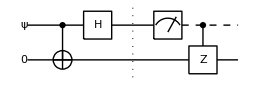

```mathematica
qc1b=QuantumCircuit[qc1a,"Separator",Measurement[S[1,3]],ControlledGate[S[1,$],S[2,3]]]
```

```mathematica
out1b=Elaborate[qc1b];
KetFactor[out1b]
```

(1_S_1⊗(c_0 0_S_2+c_1 1_S_2))/(√2)

We can rewrite the above quantum circuit using relation between the CNOT and CZ gates into the following form.

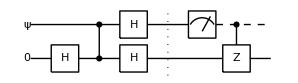

```mathematica
qc2a=QuantumCircuit[
ProductState[S[1,$]->c@{0,1},"Label"->Ket["ψ"]],Ket[S@{2}],
S[2,6],CZ[S[1,$],S[2,$]],S[{1,2},6],"Separator",
Measurement[S[1,3]],ControlledGate[S[1,$],S[2,3]]
]
```

At this stage, there is no reason why we should prefer the CZ gate to the CNOT gate. However, we will see below that the CZ gate is better suited for the measurement-based scheme.

More importantly, the Hadamard gate followed by the measurement in the standard basis on the first qubit can be regarded as a measurement in the Pauli X basis.

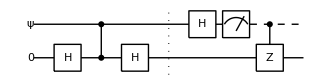

```mathematica
qc2b=QuantumCircuit[
ProductState[S[1,$]->c@{0,1},"Label"->Ket["ψ"]],Ket[S@{2}],
S[2,6],CZ[S[1,$],S[2,$]],S[2,6],"Separator",S[1,6],
Measurement[S[1,3]],ControlledGate[S[1,$],S[2,3]]
]
```

```mathematica
out2b=Elaborate[qc2b];
KetFactor[out2b]
```

(0_S_1⊗(c_0 0_S_2+c_1 1_S_2))/(√2)

It is indeed physically achieved by rotating the measurement setup, as discussed in the tutorial “Computational Model of Measurement”.  In effect, the measurement in the Pauli X basis on the first qubit transfers a quantum state to the second qubit.

Next, let us consider a slightly different quantum circuit.

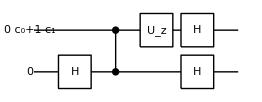
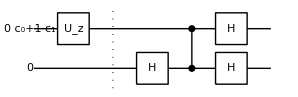
-Graphics-=-Graphics-

```mathematica
Row@{
qc3a=QuantumCircuit[ProductState[S[1]->c@{0,1}],Ket[{S[2]}],
S[2,6],CZ[S[1],S[2]],
Rotation[ϕ,S[1,3]],S[{1,2},6],
"PortSize"->{2,0.3}],
Style["=",Large],
qc3b=QuantumCircuit[ProductState[S[1]->c@{0,1}],Ket[{S[2]}],
Rotation[ϕ,S[1,3]],"Separator",
S[2,6],CZ[S[1],S[2]],S[{1,2},6],
"PortSize"->{2,0.3}]
}
```

Compared to the previous quantum circuit, this has a single-qubit rotation (Û)_z around the z-axis on the first qubit. In the above expression, the equality holds because (Û)_z commutes with the CZ gate. Applying the previous result to the quantum circuit on the right-hand side immediately gives the output state

(0⊗((Û)_z ψ)+1⊗(Ẑ(Û)_z ψ))/(√2) .

This is illustrated below.

```mathematica
out3a=Elaborate[qc3a]//TrigToExp//Garner;
KetFactor[out3a,S[1,$]]
```

0_S_1⊗((ⅇ^(-(ⅈ ϕ)/2) c_0 0_S_2)/(√2)+(ⅇ^((ⅈ ϕ)/2) c_1 1_S_2)/(√2))+1_S_1⊗((ⅇ^(-(ⅈ ϕ)/2) c_0 0_S_2)/(√2)-(ⅇ^((ⅈ ϕ)/2) c_1 1_S_2)/(√2))

Upon the measurement of the first qubit, the output state of the second qubit becomes either (Û)_z ψ or  Ẑ(Û)_z ψ depending on the measurement outcome. In either case, the state  (Û)_z ψ is achieved on the second qubit by applying an additional operation Ẑ if necessary.

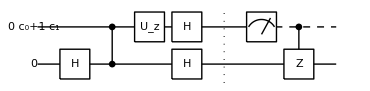

```mathematica
qc3c=QuantumCircuit[qc3a,"Separator",
Measurement[S[1,3]],ControlledGate[S[1,$],S[2,3]]]
```

```mathematica
Quiet[out3c=Elaborate[qc3c],Measurement::nonum];
KetFactor[out3c]
```

(ⅇ^(-(ⅈ ϕ)/2) 0_S_1⊗(c_0 0_S_2+ⅇ^(ⅈ ϕ) c_1 1_S_2))/(√2)

Again, the key point here is that the unitary operation (Û)_z and the Hadamard gate followed by a measurement in the standard basis on the first qubit can be regarded as a measurement in the rotated basis. In the end, we have achieved the state with unitary gate (Û)_z applied on it by means of a (rotated) measurement.

Since the Inverse of the Hadamard gate equals to the Hadamard gate itself, (Ĥ)^2=Î, one can remove the second Hadamard gate on the second qubit by applying the Hadamard gate. This leads to the following quantum circuit.

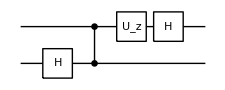

Figure 1. Elementary quantum circuit on which the measurement-based quantum computation is based.

Accounting for the extra Hadamard gate that we applied, we obtain the output state

1/(√2)Σ_(x=0,1)0⊗(Ĥ(Ẑ)^x(Û)_z ψ)

for the quantum circuit in Figure 1. This quantum circuit requires no quantum gates once an entanglement has been created by the CZ gate, and only measurement is needed. The cost is that the Hadamard gate appears as a byproduct on the output qubit. However, we will see below that the trailing Hadamard gate on the second qubit plays an important role to achieve an arbitrary single-qubit rotation in the measurement-based scheme.

Sorry, the rest is still under construction!

### Single-Qubit Rotations

### CNOT Gate

### Graph States

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Models
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪R. Raussendorf, D. Browne, and H. J. Briegel, Journal of Modern Optics 49, 1299 (2002)https://doi.org/10.1080/09500340110107487, "The one-way quantum computer--a non-network model of quantum computation (article)".
▪R. Raussendort and H. J. Briegel, Physical Review Letters 86, 5188 (2001)https://doi.org/10.1103/PhysRevLett.86.5188, "A One-Way Quantum Computer".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).